```mathematica
enV=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedHQ_NDSolve.dat"];
enVs1=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_enVs1.dat"];
enVs2=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_enVs2.dat"];
ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
```

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-10;a=1;αSch=2.;V[r_]=-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r];VCou[r_]=-α/r;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2[r_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086};
```

```mathematica
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+2.(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->50,AccuracyGoal->Infinity,PrecisionGoal->20];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
```

```mathematica
δ50[V_]:=Module[{en,len},
len=Length@ee;
Table[
en=ee[[i]];
δ50e[en,V],{i,1,len}]
]
```

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_δV.dat",δori,"Table"];
```

```mathematica
δori=δ50[V[r]];
δCou=δ50[VCou[r]];
δVs1=δ50[Vs1[r]];
δVs2=δ50[Vs2[r]];
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00021109331289576204560259811674340354226418985117) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.066307585862373919157761130262872877547524700901) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.616853) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678812766388868379805470388001760816902434956776) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.217976420664045625281029604115770451299082257979) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==1.69019) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+2.81241 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00021109331494586115082577177368087348291693850755) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+2.81241 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.066308505256787627595262371715491701289345109769) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+2.81241 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.617369) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+2.53643 Power[«2»]-3.26552 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00021109389037515242285705366432207848383411494048) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+2.53643 Power[«2»]-3.26552 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0663075663088775270940872925635466483266964331) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+2.53643 Power[«2»]-3.26552 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.616743) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

```mathematica
ΔCou=Abs[δCou-δori];
ΔVs1=Abs[δVs1-δori];
ΔVs2=Abs[δVs2-δori];
```

```mathematica
LCou=Transpose@({ee}~Join~{ΔCou});
LVs1=Transpose@({ee}~Join~{ΔVs1});
LVs2=Transpose@({ee}~Join~{ΔVs2});
```

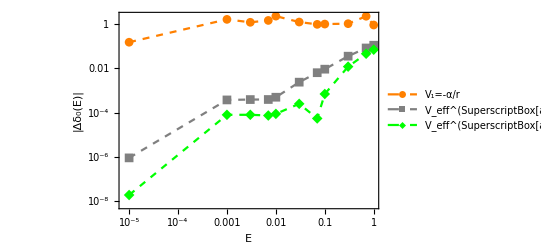

```mathematica
ListLogLogPlot[Drop[#,1]&/@{LCou,LVs1,LVs2},Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"E","|Δδ_0(E)|"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green}},PlotLegends->{"V_1=-α/r","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"}]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PS_CurveFitting_Figure3.eps",%];
```